# Визуализация. Графични обекти.

## Графика на функция на две независими променливи. Графични примитиви.

Изобразяването на графики на функции на две независими променливи става с помощта на функцията Plot3D - тя има същия принцип на действие като Plot.

```mathematica
Plot3D[x^2+y^2,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

С помощта на Graphics и съответното Graphics3D, можем да изобразяваме графични примитиви. Например отсечки, вектори, триъгълници, окръжности и др. в равнината, и съответно кубове, конуси и др. в тримерното пространство. Всеки графичен примитив, от своя страна, приема съответни аргументи, необходими за визуализацията му. Обърнете внимание на начина, по който се указват опциите на Graphics! Всички параметри се изброяват в списък, като опциите за визуализацията на всеки от графичните примитиви се поставя пред него. Опциите важат до момента в който не бъдат зададени нови. (Опитайте да премахнете опцията “Black” пред квадрата и вижте какъв ще бъде ефекта.)
В страницата на Graphics в документацията, в менюто “Details and options”, можете да видите списък с графичните примитиви, които могат са бъдат подадени на функцията. Същото се отнася и за Graphics3D.

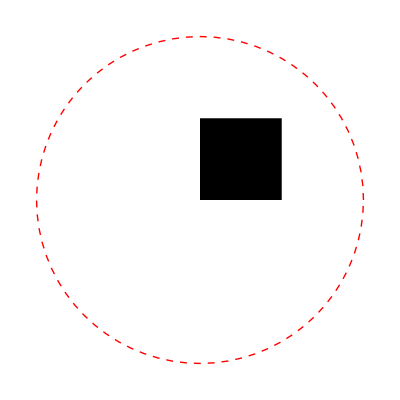

```mathematica
(*Окръжност с център (0,0) и радиус 1, изобразена с червена прекъсната линия и черен квадрат с долeн ляв ъгъл в (0,0) и горен десен ъгъл в (0.5,0.5)*)
Graphics[{Red,Dashed,Circle[{0,0},1],Black,Rectangle[{0,0},{0.5,0.5}]}]
```

Зад. 0 Дадени са точките Q(-1,1,2), R(-4,2,2) и S(-2,1,5). Намерете нормален вектор към равнината, определена от тези точки. Като използвате намерената нормала, намерете уравнението на равнината. Начертайте равнината заедно с 3-те точки, които я определят и нормалния вектор в една координатна система.

```mathematica
Q={-1,1,2};
R={-4,2,2};
S={-2,1,5};
QR=R-Q;
QS=S-Q;
normal=Cross[QR,QS];
PointInThePlane={x,y,z};
vecInThePlane=PointInThePlane-Q;
normal.vecInThePlane//Simplify
```

-8+3 x+9 y+z

```mathematica
Show[Plot3D[-3x-9y+8,{x,-5,5},{y,-5,5}],

ListPointPlot3D[{S,Q,R},PlotStyle->PointSize[0.02]], (*ListPointPlot3D е аналог на ListPlot в тримерното пространство*)

Graphics3D[{Thick,Arrowheads->0.001,Arrow[{Q,S}],Thick,Arrowheads->0.001,Arrow[{Q,R}],Arrowheads->0.02,Arrow[{Q,Q+normal}]}],

BoxRatios->Automatic
]
```

-Graphics3D-

## Графики на параметрични криви. Анимация на графични обекти.

С помощта на ParametricPlot и ParametricPlot3D, можем да изобразяваме параметрично зададени криви в 2D и 3D, съответно. Компонентите по всички направления се изброяват в списък.

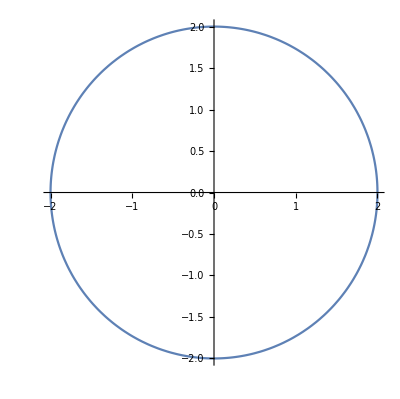

```mathematica
ParametricPlot[{2Cos[t],2Sin[t]},{t,0,2Pi}] (*Параметрично зададена окръжност с радиус 2*)
```

Manipulate[expr, {u,u_min,u_max}] пресмята стойности на expr, с възможност за интерактивна промяна на стойността на u от потребителя. Например, можем да визуализраме графика на фунцкия, зависеща от параметър, и да наблюдаваме как се изменя тя, в зависимост от стойностите на параметъра:

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]
```

Зад. 1 Циклоидата  (от гръцки: κυκλος — „окръжност“ и ειδος — „породен от“, буквално „породена от окръжността“)  е равнинна крива, описана с параметричните уравнения:

	 x = r(t- sin t),
	y = r(1 - cos t).

Тя представлява тракеторията, описана от точка от окръжност с радиус r, търкаляща се по права (напр.абсцисната ос).
(а) Да се начертае графика на циклоида, описана от окръжност с радиус 2 спрямо параметъра t, където t варира в граници от 0 до 10π.
(б) Да се анимира движението на окръжността, която описва циклоидата като първо се анимира движенеито на точката от окръжността, която “рисува” кривата в червен цвят и след това се изобрази самата окръжност;
(в) Да се анимира процеса на построяването на циклоидата.

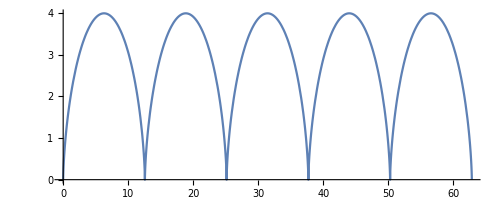

```mathematica
ParametricPlot[{2 (θ-Sin[θ]),2 (1-Cos[θ])},{θ,0,10Pi}]
```

```mathematica
Manipulate[Show[ParametricPlot[{2 (θ-Sin[θ]),2 (1-Cos[θ])},{θ,0,10Pi}],
ListPlot[{{2 (θ-Sin[θ]),2 (1-Cos[θ])}},PlotStyle->Red]],{θ,0,10Pi}]
```

```mathematica
Manipulate[Show[ParametricPlot[{2 (θ-Sin[θ]),2 (1-Cos[θ])},{θ,0,10Pi}],
ListPlot[{{2 (θ-Sin[θ]),2 (1-Cos[θ])}},PlotStyle->Red],
Graphics[Circle[{2θ,2},2]]],
{θ,0,10Pi}]
```

```mathematica
Manipulate[Show[ParametricPlot[{2 (γ-Sin[γ]),2 (1-Cos[γ])},{γ,0,θ},PlotRange->{{0,2 (10Pi-Sin[10Pi])},All}],
ListPlot[{{2 (θ-Sin[θ]),2 (1-Cos[θ])}},PlotStyle->Red],
Graphics[Circle[{θ 2,2},2]]],{θ,0.00001,10Pi}]
```

## Представяне на 3D обекти в паметта. Визуализация. Линейни трансформации.

```mathematica
ExampleData[{"Geometry3D","StanfordBunny"}]
```

-Graphics3D-

Един стандартен начин за визуализация на 3D изображения е те да се изрисуват като множество от малки триъгълници. Представени по този начин, изображенията могат да се съхраняват в компютърната памет по много удобен начин - като две матрици. Едната матрица съдържа координати на краен брой точки от повърхнината, която трябва да се изрисува (тези точки предсатвяляват върховете на триъгълниците), а другата - наредени тройки с индекси от първата матрица, всяка от които определя един триъгълник. Stanford Bunny се състои от 69,451 триъгълника, които са получени с помощта на 3D сканиране на керамично зайче. Това е стандартен модел за тестване на различни графични алгоритми - например заглаждане, компресия и др.

```mathematica
vertexData=ExampleData[{"Geometry3D","StanfordBunny"},"VertexData"];
polyData=ExampleData[{"Geometry3D","StanfordBunny"},"PolygonData"];
Graphics3D[GraphicsComplex[vertexData,Polygon[polyData]]]
```

-Graphics3D-

При полет, самолетите могат да се завъртат в 3 направления :
	Roll (надлъжна ос)-въртене около ос, минаваща през носа и опашката на самолета;
	Pitch (напречна ос)-отклонение на носа нагоре/надолу от ос, минаваща през двете крила на самолета; 
	Yaw (вертикална ос)-отклонение наляво/надясно от ос, ортогонална на другите две оси (вертиклана);
Промяната в курса на самолета се осъществява чрез завъртане под определен ъгъл спрямо някоя от тези три оси. Тези дефиниции са възприети за употреба и при движението на космически кораби.

                                                                  -Graphics-
	
Зад. 2 Да се зареди тримерното изображение на космическа совалка от базата данни на ситемата Mathematica, с помощта на ExampleData[{"Geometry3D","SpaceShuttle"}].
Да се извелкат данните за триунгалуцаията на изображението и да се извършат с него следните трансформации:
	(a) Да се изобрази завъртането на самолета под ъгъл 30°, относно оста roll;
	(б) Да се изобрази завъртането на самолета под ъгъл 30°, относно оста yaw;
	(в) Да се направи композиция на завъртанията от подусловия (a) и (б);
	(г) Да се анимира пълно завъртане на совалката около оста roll;
	(д) Да се анимира пълното завъртане на совалката около оста yaw;

```mathematica
ExampleData[{"Geometry3D","SpaceShuttle"}]
```

-Graphics3D-

```mathematica
dataVert=ExampleData[{"Geometry3D","SpaceShuttle"},"VertexData"];
dataPoly=ExampleData[{"Geometry3D","SpaceShuttle"},"PolygonData"];
```

```mathematica
(*roll, pitch, yaw - x, y, z*)
```

```mathematica
Graphics3D[GraphicsComplex[dataVert,Polygon[dataPoly]],Axes->True,(* AxesOrigin-> {0,0,0},*)AxesLabel->{"Roll","Pitch","Yaw"},LabelStyle->Directive[Bold, Medium],AxesStyle->Thick]
```

-Graphics3D-

```mathematica
(*roll 30deg - about x-axIs*)
Graphics3D[GraphicsComplex[Table[{{1,0,0},{0,Cos[Pi/6],-Sin[Pi/6]},{0,Sin[Pi/6],Cos[Pi/6]}}.dataVert[[i]],{i,1,Length[dataVert]}],Polygon[dataPoly]],AxesLabel->{"Roll","Pitch","Yaw"},Axes->True]
```

-Graphics3D-

```mathematica
(*full rotation about roll*)
Manipulate[Graphics3D[GraphicsComplex[Table[{{1,0,0},{0,Cos[k],-Sin[k]},{0,Sin[k],Cos[k]}}.dataVert[[i]],{i,1,Length[dataVert]}],Polygon[dataPoly]],Boxed->False, PlotRange->All],{k,0,2Pi}]
```

С подусловия (б), (в) и (д) опитайте сами. :)

Зад.3  Да се визулизират следните две тела в една координатна система:
	(а) Куб, единият от ъглите на който е разположен в т. (0,0,0), ръбовете му са успоредни на коориднатните оси и имат дължина 1;
	(б) Кълбо с център (0,0,0) и радиус 1.
Да се визуализира сечението на двете тела и да се намери обема му.

```mathematica
(*Ball и Cuboid са графични примитиви. Те не са зададени като геометрични области, с които можем да правим пресмятания.*)
ball=Ball[{0,0,0},1]; 
cube=Cuboid[{0,0,0},{1,1,1}];
```

```mathematica
Graphics3D[{ball,cube}]
```

-Graphics3D-

```mathematica
(*RegionMember ще върне израз с булеви условия за координатите на точките, попадащи в областите от пространството, определени от тези тела. Имайки това пердставяне, можем вече да намерим сечението им.*)
RegionMember[ball,{x,y,z}]
RegionMember[cube,{x,y,z}]
```

(x|y|z)∈Reals&&x^2+y^2+z^2≤1

(x|y|z)∈Reals&&0≤x≤1&&0≤y≤1&&0≤z≤1

```mathematica
ballRegion=ImplicitRegion[RegionMember[ball,{x,y,z}],{x,y,z}];
cubeRegion=ImplicitRegion[RegionMember[cube,{x,y,z}],{x,y,z}];

cubePlot=RegionPlot3D[{ballRegion,cubeRegion},Axes->True]
```

-Graphics3D-

```mathematica
RegionPlot3D[RegionIntersection[ballRegion,cubeRegion]]
```

-Graphics3D-

```mathematica
Volume[RegionIntersection[ballRegion,cubeRegion]]
```

π/6